# Minimizing Functionals (RBF approach) J (y) = (y(x) - f_0(x))^2+a f_1(|y’(x)|) + b f_2(|y’’(x)|)

## Defining functions f_1, f_2 , f_3 and weight constants a & b

```mathematica
Clear[x,x1,x2,x3,x4,L,f0,f1,f2,a,b,y,u];
f0[x_]=Sqrt[1+x^2] ;
f1[x_]=x;
f2[x_]=Exp[x];
(*Lagrangian constants*)
a=1.;
b=1.;
```

## Computing Lagrangian and left side of Euler-Lagrange equation

```mathematica
Print["Lagrangian:"]
Lag[x1_,x2_,x3_,x4_]=(x2-f0[x1])^2+a f1[Sqrt[x3^2]]+b f2[Sqrt[x4^2]]
Print["Real lagrangian"]
L[x_]=Lag[x,y[x],y'[x],y''[x]]
Ly[x_]=D[Lag[x1,x2,x3,x4], x2]/.x1->x/.x2->y[x]/.x3->y'[x]/.x4->y''[x];
Lyx[x_]=D[Lag[x1,x2,x3,x4], x3]/.x1->x/.x2->y[x]/.x3->y'[x]/.x4->y''[x];
Lyxx[x_]=D[Lag[x1,x2,x3,x4], x4]/.x1->x/.x2->y[x]/.x3->y'[x]/.x4->y''[x];
Print["Left side of EL equation"]
EL[x_]=Ly[x]-Lyx'[x]+Lyxx''[x]//FullSimplify (*left side of Euler-Lagrange equation*)
```

Lagrangian:

0.+(-√(1+x1^2)+x2)^2+0. √(x3^2)

Real lagrangian

0.+(-√(1+x^2)+y[x])^2+0. √(y'[x]^2)

Left side of EL equation

2 (-√(1+x^2)+y[x])

## Defining RBF to occupy and u(x) = Σc_j ϕ(|x-x_j|)

```mathematica
(*Number of RBF's*)
n=3;
(*Colocation points are linearly spaced*)
Col=Range[0,1,1/(n-1)];
(* Shape parameter *)
ϵ=1.0; 
(*RBF function*)
ϕ[r_]=Exp[-(ϵ r)^2];
Print["u[x] function"]
u[x_]=∑_(j=1)^n Subscript[c, j] ϕ[√((x-Col[[j]])^2)]
```

u[x] function

ⅇ^(-1. x^2) c_1+ⅇ^(-1. (-1/2+x)^2) c_2+ⅇ^(-1. (-1+x)^2) c_3

## Replacing y(x)->u(x) in EL equation and evaluation on interior points of domain

```mathematica
out1=EL[x]/.y->u;
Eq=RandomReal[{0,1},n-2];
For[i=1,i<=n-2,i++,
Eq[[i]]=out1/.x->Col[[i+1]] //FullSimplify	
]
```

## Solving the non-linear system of equations: Approach 1, Newton Method

{c_1→1.84511,c_2→-2.26624,c_3→2.50039}

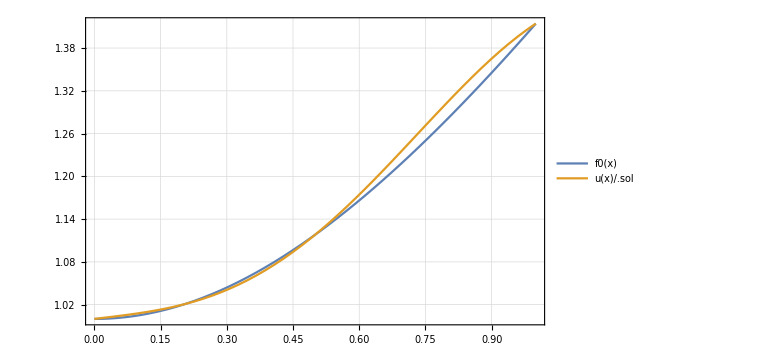

```mathematica
F=Join[{u[0]-f0[0],u[1]-f0[1]},Eq];
sol=FindRoot[F,{{Subscript[c, 1],1},{Subscript[c, 2],2},{Subscript[c, 3],3}},Method->{"Newton","UpdateJacobian"->1},MaxIterations->100]
nsol={Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]}/.sol;(*Numeric solution*)
Plot[{f0[x],u[x]/.sol},{x,0,1},PlotTheme->"Detailed",ImageSize->Large]
```

## Solving the non-linear system of equations: Approach 2, Dynamic System Applying the trick of made coefficients c_j dependant of time -> c_j(t)

### Time dependence trick

```mathematica
Subscript[u, t][x_]=u[x]/.{Subscript[c, 1]->Subscript[c, 1][t],Subscript[c, 2]->Subscript[c, 2][t],Subscript[c, 3]->Subscript[c, 3][t]}
Subscript[Eq, t]=Eq/.{Subscript[c, 1]->Subscript[c, 1][t],Subscript[c, 2]->Subscript[c, 2][t],Subscript[c, 3]->Subscript[c, 3][t]};
```

ⅇ^(-1. x^2) c_1[t]+ⅇ^(-1. (-1/2+x)^2) c_2[t]+ⅇ^(-1. (-1+x)^2) c_3[t]

### Dirty way to choose α , β and γ to ensure convergence

```mathematica
(*Choosing α, β and γ*)
Clear[F,α,β,γ];

(*Redefining vectorial field*)
Print["Vectorial Field"]
F={α(u[0]-f0[0]),β(u[1]-f0[1]),γ Eq[[1]]}

(*Jacobian*) 
DF=D[F,{{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]}}];

(*Eigenvalues at stationary point*)
EVs=Eigenvalues[DF/.sol];

(*Reduce[Max[Re[EVs]]<0 && -5.≤α≤5. && -5.≤β≤5. && -5.≤γ≤5.,{α,β,γ}]*)

(*Dirty trick*)
l=10.;
While[True,
α=RandomReal[{-l,l}];
β=RandomReal[{-l,l}];
γ=RandomReal[{-l,l}];
If[Max[Re[EVs]]<0,Break[]];
]
Print["Values of α,β,γ where real part of eigenvalues is negative"]
{α,β,γ,Max[Re[EVs]]}
```

Vectorial Field

{α (-1+1. c_1+0.778801 c_2+0.367879 c_3),β (-√2+0.367879 c_1+0.778801 c_2+1. c_3),γ (-√5+1.5576 c_1+2. c_2+1.5576 c_3+1/(-0.778801 c_1-2. c_2-0.778801 c_3)ⅇ^(√((0.778801 c_1+2. c_2+0.778801 c_3)^2)) (15.1633 (1. c_1-1. c_3)^2 √((0.778801 c_1+2. c_2+0.778801 c_3)^2)-0.606531 (1. c_1+2.56805 c_2+1. c_3) (1. c_1+15.4083 c_2+1. c_3)))}

Values of α,β,γ where real part of eigenvalues is negative

{-7.47353,9.45119,8.03964,-5.36592}

### Solving the dynamic system ∂c̲=F(c̲)

General::ovfl: Overflow occurred in computation.

NDSolve::nlnum: The function value {-7.8797289241419×10^317, 2.70780205618749×10^318, Overflow[]} is not a list of numbers with dimensions {3} at {t, c_1[t], c_2[t], c_3[t]} = {1.34208×10^-6, -4.39257982793108×10^313, 1.50991710727142×10^314, 2.86402383453554×10^317}.

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

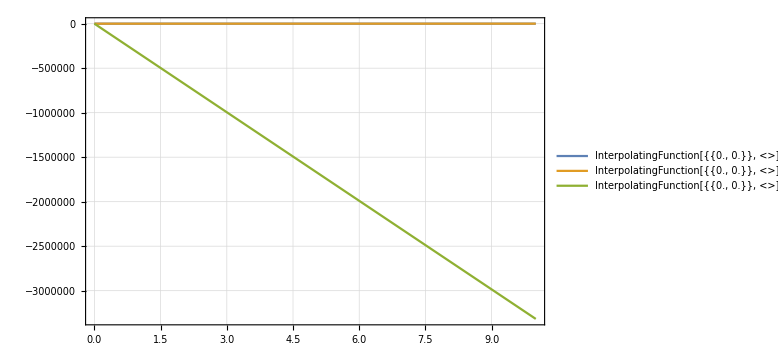

Solution c_1[t],c_2[t],c_3[t] at t->∞

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{{-197.888,333.857,-3.31727×10^6}}

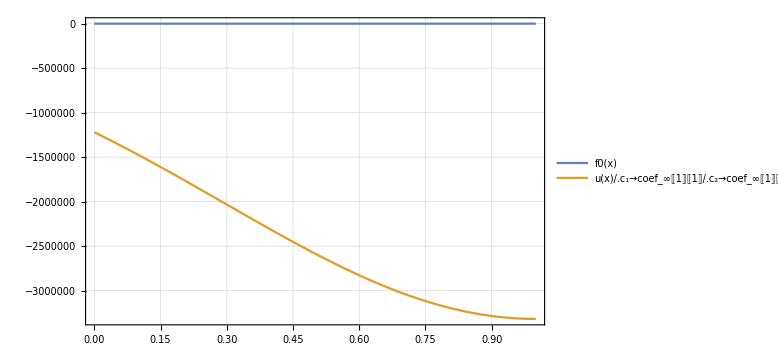

-Graphics3D-

-Graphics3D-

```mathematica
(*Solving the dynamic system*)
Subscript[T, F]=10;
s=NDSolve[{
α(Subscript[u, t][0]-f0[0])==Subscript[c, 1]'[t],
β(Subscript[u, t][1]-f0[1])==Subscript[c, 2]'[t],
γ Subscript[Eq, t][[1]]==Subscript[c, 3]'[t],
Subscript[c, 1][0]==1,
Subscript[c, 2][0]==2,
Subscript[c, 3][0]==3},
{Subscript[c, 1][t],Subscript[c, 2][t],Subscript[c, 3][t]},{t,0,Subscript[T, F]=10},
Method->"ImplicitRungeKutta"];

(*Plot of solutions*)
Plot[Evaluate[{Subscript[c, 1][t],Subscript[c, 2][t],Subscript[c, 3][t]}/.s],{t,0,Subscript[T, F]},PlotTheme->"Detailed",ImageSize->Large]
Print["Solution c_1[t],c_2[t],c_3[t] at t->∞"]
Subscript[coef, ∞]={Subscript[c, 1][t],Subscript[c, 2][t],Subscript[c, 3][t]}/.s/.t->Subscript[T, F]


(*Plot of final solution*)
Plot[{f0[x],u[x]/.Subscript[c, 1]->Subscript[coef, ∞][[1]][[1]]/.Subscript[c, 2]->Subscript[coef, ∞][[1]][[2]]/.Subscript[c, 3]->Subscript[coef, ∞][[1]][[3]]},{x,0,1},PlotTheme->"Detailed",ImageSize->Large]

(*Plot of vector fields*)
ws=0.5; (*Window size of VectorPlot3D around F(Subscript[c, 0])=0*)
VectorPlot3D[{u[0]-f0[0],u[1]-f0[1], Eq[[1]]},{Subscript[c, 1],nsol[[1]]-ws,nsol[[1]]+ws},{Subscript[c, 2],nsol[[2]]-ws,nsol[[2]]+ws},{Subscript[c, 3],nsol[[3]]-ws,nsol[[3]]+ws},PlotLabel->"F[c] without factors",ImageSize->Large]
VectorPlot3D[{α(u[0]-f0[0]),β(u[1]-f0[1]), γ Eq[[1]]},{Subscript[c, 1],nsol[[1]]-ws,nsol[[1]]+ws},{Subscript[c, 2],nsol[[2]]-ws,nsol[[2]]+ws},{Subscript[c, 3],nsol[[3]]-ws,nsol[[3]]+ws},PlotLabel->"F[c] with factors",ImageSize->Large]
```